```mathematica
2+2
```

4

```mathematica
?FindFit
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
deglist={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933};
```

```mathematica
degfreq={0,51,86,106,148,183,170,183,228,224,245,256,188,196,157,197,125,141,128,109,131,119,84,95,83,112,70,76,73,71,66,49,44,44,57,43,48,40,61,60,38,45,39,31,38,27,39,22,58,35,30,18,22,20,32,25,25,16,27,29,23,21,19,10,22,16,26,16,24,20,18,13,14,29,12,7,12,17,16,20,16,14,8,12,14,10,15,14,9,36,11,9,10,5,13,6,5,11,7,4,8,6,8,3,4,6,9,4,8,6,10,6,3,3,6,2,4,4,9,6,11,2,5,7,4,6,6,6,9,2,7,2,2,4,5,4,5,5,6,6,6,3,10,5,3,7,3,4,4,5,4,4,7,3,1,0,3,4,3,2,0,2,4,2,6,1,4,3,0,6,1,5,3,1,0,5,4,1,2,1,2,3,3,3,3,3,1,5,2,3,3,3,1,1,0,3,2,1,1,1,4,3,0,1,3,1,7,0,4,1,3,2,2,1,2,1,1,1,2,0,1,2,2,0,1,2,0,0,6,1,1,1,1,2,2,3,2,0,3,2,0,1,3,1,3,0,2,0,0,0,1,2,1,4,2,0,0,2,2,1,1,2,2,3,1,1,1,0,1,0,1,1,0,1,0,1,0,3,0,2,2,3,2,1,1,0,1,0,0,1,0,0,1,0,1,0,3,0,1,2,1,1,2,0,2,0,0,0,0,0,0,1,0,0,0,2,2,0,1,1,0,1,0,0,1,0,0,0,0,3,1,0,1,3,1,1,0,1,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,2,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,0,0,1,0,1,0,0,1,3,0,3,0,1,1,0,0,0,0,0,0,0,0,1,0,0,2,1,0,0,1,1,1,0,0,0,1,1,0,2,1,1,0,0,1,1,0,0,1,0,0,1,1,0,0,3,0,0,1,0,2,1,1,0,0,1,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,1,2,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,2,0,0,1,0,0,1,0,0,0,0,1,0,2,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1};
```

```mathematica
mat={deglist,degfreq};
```

```mathematica
data=Transpose[mat]
```

{{0,0},{1,51},{2,86},{3,106},{4,148},{5,183},{6,170},{7,183},{8,228},{9,224},{10,245},{11,256},{12,188},{13,196},{14,157},{15,197},{16,125},{17,141},{18,128},{19,109},{20,131},{21,119},{22,84},{23,95},{24,83},{25,112},{26,70},{27,76},{28,73},{29,71},{30,66},{31,49},{32,44},{33,44},{34,57},{35,43},{36,48},{37,40},{38,61},{39,60},{40,38},{41,45},{42,39},{43,31},{44,38},{45,27},{46,39},{47,22},{48,58},{49,35},{50,30},{51,18},{52,22},{53,20},{54,32},{55,25},{56,25},{57,16},{58,27},{59,29},{60,23},{61,21},{62,19},{63,10},{64,22},{65,16},{66,26},{67,16},{68,24},{69,20},{70,18},{71,13},{72,14},{73,29},{74,12},{75,7},{76,12},{77,17},{78,16},{79,20},{80,16},{81,14},{82,8},{83,12},{84,14},{85,10},{86,15},{87,14},{88,9},{89,36},{90,11},{91,9},{92,10},{93,5},{94,13},{95,6},{96,5},{97,11},{98,7},{99,4},{100,8},{101,6},{102,8},{103,3},{104,4},{105,6},{106,9},{107,4},{108,8},{109,6},{110,10},{111,6},{112,3},{113,3},{114,6},{115,2},{116,4},{117,4},{118,9},{119,6},{120,11},{121,2},{122,5},{123,7},{124,4},{125,6},{126,6},{127,6},{128,9},{129,2},{130,7},{131,2},{132,2},{133,4},{134,5},{135,4},{136,5},{137,5},{138,6},{139,6},{140,6},{141,3},{142,10},{143,5},{144,3},{145,7},{146,3},{147,4},{148,4},{149,5},{150,4},{151,4},{152,7},{153,3},{154,1},{155,0},{156,3},{157,4},{158,3},{159,2},{160,0},{161,2},{162,4},{163,2},{164,6},{165,1},{166,4},{167,3},{168,0},{169,6},{170,1},{171,5},{172,3},{173,1},{174,0},{175,5},{176,4},{177,1},{178,2},{179,1},{180,2},{181,3},{182,3},{183,3},{184,3},{185,3},{186,1},{187,5},{188,2},{189,3},{190,3},{191,3},{192,1},{193,1},{194,0},{195,3},{196,2},{197,1},{198,1},{199,1},{200,4},{201,3},{202,0},{203,1},{204,3},{205,1},{206,7},{207,0},{208,4},{209,1},{210,3},{211,2},{212,2},{213,1},{214,2},{215,1},{216,1},{217,1},{218,2},{219,0},{220,1},{221,2},{222,2},{223,0},{224,1},{225,2},{226,0},{227,0},{228,6},{229,1},{230,1},{231,1},{232,1},{233,2},{234,2},{235,3},{236,2},{237,0},{238,3},{239,2},{240,0},{241,1},{242,3},{243,1},{244,3},{245,0},{246,2},{247,0},{248,0},{249,0},{250,1},{251,2},{252,1},{253,4},{254,2},{255,0},{256,0},{257,2},{258,2},{259,1},{260,1},{261,2},{262,2},{263,3},{264,1},{265,1},{266,1},{267,0},{268,1},{269,0},{270,1},{271,1},{272,0},{273,1},{274,0},{275,1},{276,0},{277,3},{278,0},{279,2},{280,2},{281,3},{282,2},{283,1},{284,1},{285,0},{286,1},{287,0},{288,0},{289,1},{290,0},{291,0},{292,1},{293,0},{294,1},{295,0},{296,3},{297,0},{298,1},{299,2},{300,1},{301,1},{302,2},{303,0},{304,2},{305,0},{306,0},{307,0},{308,0},{309,0},{310,0},{311,1},{312,0},{313,0},{314,0},{315,2},{316,2},{317,0},{318,1},{319,1},{320,0},{321,1},{322,0},{323,0},{324,1},{325,0},{326,0},{327,0},{328,0},{329,3},{330,1},{331,0},{332,1},{333,3},{334,1},{335,1},{336,0},{337,1},{338,0},{339,0},{340,0},{341,0},{342,1},{343,0},{344,1},{345,0},{346,0},{347,1},{348,0},{349,1},{350,1},{351,0},{352,1},{353,0},{354,0},{355,1},{356,1},{357,0},{358,0},{359,2},{360,0},{361,0},{362,0},{363,0},{364,0},{365,1},{366,1},{367,0},{368,0},{369,0},{370,0},{371,0},{372,1},{373,0},{374,0},{375,0},{376,1},{377,1},{378,0},{379,1},{380,1},{381,1},{382,1},{383,0},{384,1},{385,0},{386,0},{387,1},{388,0},{389,1},{390,0},{391,0},{392,1},{393,3},{394,0},{395,3},{396,0},{397,1},{398,1},{399,0},{400,0},{401,0},{402,0},{403,0},{404,0},{405,0},{406,0},{407,1},{408,0},{409,0},{410,2},{411,1},{412,0},{413,0},{414,1},{415,1},{416,1},{417,0},{418,0},{419,0},{420,1},{421,1},{422,0},{423,2},{424,1},{425,1},{426,0},{427,0},{428,1},{429,1},{430,0},{431,0},{432,1},{433,0},{434,0},{435,1},{436,1},{437,0},{438,0},{439,3},{440,0},{441,0},{442,1},{443,0},{444,2},{445,1},{446,1},{447,0},{448,0},{449,1},{450,0},{451,1},{452,1},{453,0},{454,0},{455,0},{456,0},{457,1},{458,0},{459,0},{460,1},{461,0},{462,0},{463,0},{464,0},{465,1},{466,0},{467,0},{468,0},{469,0},{470,0},{471,0},{472,0},{473,0},{474,0},{475,0},{476,0},{477,0},{478,0},{479,0},{480,0},{481,0},{482,2},{483,0},{484,1},{485,0},{486,0},{487,0},{488,1},{489,2},{490,0},{491,0},{492,0},{493,0},{494,1},{495,0},{496,0},{497,1},{498,0},{499,0},{500,0},{501,0},{502,1},{503,0},{504,0},{505,0},{506,0},{507,0},{508,0},{509,0},{510,0},{511,1},{512,1},{513,0},{514,0},{515,0},{516,1},{517,0},{518,0},{519,0},{520,0},{521,0},{522,1},{523,0},{524,0},{525,0},{526,2},{527,0},{528,0},{529,1},{530,0},{531,0},{532,1},{533,0},{534,0},{535,0},{536,0},{537,1},{538,0},{539,2},{540,0},{541,1},{542,1},{543,0},{544,0},{545,0},{546,0},{547,0},{548,0},{549,0},{550,1},{551,0},{552,0},{553,0},{554,0},{555,0},{556,0},{557,0},{558,0},{559,0},{560,0},{561,0},{562,0},{563,0},{564,0},{565,0},{566,0},{567,0},{568,0},{569,0},{570,0},{571,0},{572,0},{573,0},{574,0},{575,0},{576,0},{577,0},{578,0},{579,0},{580,0},{581,2},{582,0},{583,0},{584,0},{585,1},{586,0},{587,0},{588,0},{589,1},{590,1},{591,0},{592,0},{593,0},{594,0},{595,0},{596,0},{597,0},{598,0},{599,0},{600,0},{601,0},{602,0},{603,0},{604,0},{605,0},{606,0},{607,1},{608,0},{609,0},{610,1},{611,0},{612,0},{613,0},{614,0},{615,0},{616,0},{617,0},{618,0},{619,1},{620,1},{621,0},{622,0},{623,0},{624,0},{625,0},{626,0},{627,0},{628,0},{629,0},{630,0},{631,0},{632,0},{633,0},{634,0},{635,0},{636,0},{637,0},{638,1},{639,0},{640,0},{641,1},{642,0},{643,1},{644,0},{645,0},{646,0},{647,0},{648,0},{649,0},{650,0},{651,0},{652,0},{653,0},{654,0},{655,0},{656,0},{657,0},{658,1},{659,0},{660,0},{661,0},{662,0},{663,0},{664,0},{665,0},{666,0},{667,0},{668,1},{669,0},{670,0},{671,0},{672,0},{673,0},{674,0},{675,0},{676,0},{677,0},{678,0},{679,0},{680,0},{681,0},{682,0},{683,0},{684,0},{685,0},{686,0},{687,0},{688,0},{689,0},{690,0},{691,0},{692,0},{693,0},{694,0},{695,0},{696,0},{697,0},{698,0},{699,0},{700,0},{701,0},{702,0},{703,1},{704,0},{705,1},{706,0},{707,0},{708,0},{709,0},{710,0},{711,1},{712,0},{713,0},{714,0},{715,0},{716,0},{717,1},{718,1},{719,0},{720,0},{721,0},{722,0},{723,0},{724,0},{725,0},{726,0},{727,0},{728,0},{729,0},{730,0},{731,0},{732,0},{733,0},{734,0},{735,0},{736,1},{737,0},{738,0},{739,0},{740,0},{741,0},{742,0},{743,0},{744,0},{745,0},{746,0},{747,0},{748,0},{749,0},{750,0},{751,0},{752,0},{753,0},{754,1},{755,0},{756,0},{757,0},{758,0},{759,0},{760,0},{761,0},{762,0},{763,0},{764,0},{765,0},{766,0},{767,0},{768,0},{769,0},{770,0},{771,0},{772,0},{773,0},{774,0},{775,0},{776,0},{777,0},{778,0},{779,0},{780,0},{781,0},{782,0},{783,0},{784,0},{785,0},{786,0},{787,0},{788,0},{789,0},{790,0},{791,0},{792,0},{793,0},{794,0},{795,0},{796,0},{797,0},{798,0},{799,0},{800,1},{801,0},{802,0},{803,0},{804,0},{805,0},{806,0},{807,0},{808,0},{809,1},{810,0},{811,0},{812,0},{813,0},{814,0},{815,0},{816,0},{817,0},{818,0},{819,0},{820,0},{821,0},{822,0},{823,0},{824,0},{825,0},{826,0},{827,0},{828,0},{829,0},{830,0},{831,0},{832,0},{833,0},{834,0},{835,0},{836,0},{837,0},{838,0},{839,0},{840,0},{841,0},{842,0},{843,0},{844,0},{845,0},{846,0},{847,0},{848,0},{849,0},{850,0},{851,0},{852,0},{853,1},{854,0},{855,0},{856,0},{857,1},{858,0},{859,0},{860,0},{861,0},{862,0},{863,0},{864,0},{865,0},{866,0},{867,0},{868,0},{869,0},{870,0},{871,0},{872,0},{873,0},{874,0},{875,0},{876,0},{877,0},{878,1},{879,0},{880,0},{881,0},{882,0},{883,0},{884,0},{885,0},{886,0},{887,0},{888,0},{889,0},{890,0},{891,0},{892,0},{893,0},{894,0},{895,0},{896,0},{897,0},{898,0},{899,0},{900,0},{901,0},{902,0},{903,0},{904,0},{905,0},{906,0},{907,0},{908,0},{909,0},{910,0},{911,0},{912,0},{913,0},{914,0},{915,0},{916,0},{917,0},{918,0},{919,0},{920,1},{921,0},{922,1},{923,0},{924,0},{925,0},{926,0},{927,0},{928,0},{929,0},{930,0},{931,0},{932,0},{933,0},{934,0},{935,0},{936,0},{937,0},{938,1},{939,0},{940,0},{941,0},{942,0},{943,0},{944,0},{945,0},{946,0},{947,0},{948,0},{949,0},{950,0},{951,0},{952,0},{953,0},{954,0},{955,0},{956,0},{957,0},{958,0},{959,0},{960,0},{961,0},{962,0},{963,0},{964,0},{965,0},{966,1},{967,0},{968,0},{969,0},{970,0},{971,1},{972,0},{973,0},{974,0},{975,0},{976,0},{977,0},{978,1},{979,0},{980,0},{981,0},{982,0},{983,0},{984,0},{985,0},{986,0},{987,1},{988,0},{989,0},{990,0},{991,0},{992,0},{993,0},{994,0},{995,0},{996,0},{997,0},{998,0},{999,0},{1000,0},{1001,0},{1002,0},{1003,0},{1004,0},{1005,0},{1006,0},{1007,0},{1008,0},{1009,0},{1010,0},{1011,0},{1012,0},{1013,0},{1014,1},{1015,0},{1016,0},{1017,0},{1018,0},{1019,0},{1020,0},{1021,0},{1022,0},{1023,0},{1024,0},{1025,0},{1026,0},{1027,0},{1028,0},{1029,1},{1030,0},{1031,0},{1032,0},{1033,0},{1034,0},{1035,0},{1036,0},{1037,0},{1038,0},{1039,0},{1040,0},{1041,0},{1042,1},{1043,0},{1044,0},{1045,1},{1046,0},{1047,0},{1048,0},{1049,0},{1050,0},{1051,0},{1052,0},{1053,0},{1054,0},{1055,1},{1056,0},{1057,0},{1058,0},{1059,0},{1060,0},{1061,0},{1062,0},{1063,0},{1064,0},{1065,0},{1066,1},{1067,0},{1068,0},{1069,0},{1070,0},{1071,0},{1072,0},{1073,0},{1074,0},{1075,0},{1076,0},{1077,0},{1078,0},{1079,1},{1080,1},{1081,0},{1082,0},{1083,0},{1084,0},{1085,0},{1086,0},{1087,0},{1088,0},{1089,0},{1090,0},{1091,0},{1092,1},{1093,1},{1094,1},{1095,1},{1096,0},{1097,0},{1098,0},{1099,0},{1100,0},{1101,0},{1102,0},{1103,0},{1104,1},{1105,0},{1106,0},{1107,0},{1108,0},{1109,0},{1110,0},{1111,0},{1112,0},{1113,0},{1114,0},{1115,0},{1116,0},{1117,0},{1118,0},{1119,0},{1120,0},{1121,0},{1122,0},{1123,0},{1124,0},{1125,0},{1126,0},{1127,0},{1128,0},{1129,0},{1130,0},{1131,0},{1132,0},{1133,0},{1134,0},{1135,0},{1136,0},{1137,0},{1138,0},{1139,0},{1140,0},{1141,0},{1142,0},{1143,0},{1144,0},{1145,0},{1146,0},{1147,0},{1148,0},{1149,0},{1150,0},{1151,0},{1152,0},{1153,0},{1154,0},{1155,0},{1156,0},{1157,0},{1158,0},{1159,0},{1160,0},{1161,0},{1162,0},{1163,0},{1164,0},{1165,0},{1166,0},{1167,0},{1168,0},{1169,0},{1170,0},{1171,0},{1172,0},{1173,0},{1174,0},{1175,0},{1176,1},{1177,0},{1178,0},{1179,0},{1180,0},{1181,0},{1182,0},{1183,0},{1184,0},{1185,0},{1186,0},{1187,0},{1188,0},{1189,0},{1190,0},{1191,0},{1192,0},{1193,0},{1194,0},{1195,0},{1196,0},{1197,0},{1198,0},{1199,0},{1200,0},{1201,0},{1202,0},{1203,0},{1204,0},{1205,0},{1206,0},{1207,0},{1208,0},{1209,0},{1210,0},{1211,0},{1212,0},{1213,0},{1214,0},{1215,0},{1216,0},{1217,0},{1218,0},{1219,0},{1220,0},{1221,0},{1222,0},{1223,0},{1224,0},{1225,0},{1226,0},{1227,0},{1228,0},{1229,0},{1230,0},{1231,0},{1232,0},{1233,0},{1234,0},{1235,0},{1236,0},{1237,0},{1238,0},{1239,0},{1240,0},{1241,0},{1242,0},{1243,0},{1244,1},{1245,0},{1246,0},{1247,0},{1248,0},{1249,0},{1250,0},{1251,0},{1252,0},{1253,0},{1254,0},{1255,0},{1256,0},{1257,0},{1258,0},{1259,0},{1260,0},{1261,0},{1262,0},{1263,1},{1264,0},{1265,0},{1266,0},{1267,0},{1268,0},{1269,0},{1270,0},{1271,0},{1272,0},{1273,0},{1274,0},{1275,0},{1276,0},{1277,0},{1278,0},{1279,0},{1280,1},{1281,0},{1282,0},{1283,0},{1284,0},{1285,0},{1286,0},{1287,0},{1288,0},{1289,1},{1290,0},{1291,0},{1292,0},{1293,0},{1294,0},{1295,0},{1296,0},{1297,0},{1298,0},{1299,0},{1300,0},{1301,0},{1302,0},{1303,0},{1304,0},{1305,0},{1306,0},{1307,0},{1308,0},{1309,0},{1310,0},{1311,0},{1312,0},{1313,0},{1314,0},{1315,0},{1316,0},{1317,0},{1318,0},{1319,0},{1320,0},{1321,0},{1322,0},{1323,0},{1324,0},{1325,0},{1326,0},{1327,0},{1328,0},{1329,0},{1330,0},{1331,0},{1332,0},{1333,0},{1334,0},{1335,0},{1336,0},{1337,0},{1338,0},{1339,0},{1340,0},{1341,0},{1342,0},{1343,0},{1344,0},{1345,1},{1346,0},{1347,0},{1348,0},{1349,0},{1350,0},{1351,0},{1352,0},{1353,0},{1354,0},{1355,0},{1356,0},{1357,0},{1358,0},{1359,0},{1360,0},{1361,0},{1362,0},{1363,0},{1364,0},{1365,0},{1366,0},{1367,0},{1368,0},{1369,0},{1370,0},{1371,1},{1372,0},{1373,0},{1374,0},{1375,0},{1376,0},{1377,0},{1378,0},{1379,0},{1380,0},{1381,0},{1382,0},{1383,0},{1384,0},{1385,0},{1386,1},{1387,0},{1388,0},{1389,0},{1390,0},{1391,0},{1392,0},{1393,0},{1394,1},{1395,0},{1396,0},{1397,0},{1398,0},{1399,0},{1400,0},{1401,0},{1402,0},{1403,0},{1404,0},{1405,0},{1406,0},{1407,0},{1408,0},{1409,0},{1410,0},{1411,0},{1412,0},{1413,0},{1414,0},{1415,0},{1416,0},{1417,0},{1418,0},{1419,0},{1420,0},{1421,0},{1422,0},{1423,0},{1424,0},{1425,0},{1426,1},{1427,0},{1428,0},{1429,0},{1430,0},{1431,0},{1432,0},{1433,0},{1434,0},{1435,0},{1436,0},{1437,0},{1438,0},{1439,0},{1440,0},{1441,0},{1442,0},{1443,0},{1444,0},{1445,0},{1446,0},{1447,0},{1448,0},{1449,0},{1450,0},{1451,0},{1452,0},{1453,0},{1454,0},{1455,0},{1456,0},{1457,0},{1458,0},{1459,0},{1460,0},{1461,0},{1462,0},{1463,0},{1464,0},{1465,0},{1466,0},{1467,0},{1468,0},{1469,0},{1470,0},{1471,0},{1472,0},{1473,0},{1474,0},{1475,0},{1476,0},{1477,0},{1478,0},{1479,0},{1480,0},{1481,0},{1482,0},{1483,0},{1484,0},{1485,0},{1486,0},{1487,0},{1488,0},{1489,0},{1490,0},{1491,0},{1492,0},{1493,0},{1494,0},{1495,0},{1496,0},{1497,0},{1498,0},{1499,0},{1500,0},{1501,0},{1502,0},{1503,0},{1504,0},{1505,0},{1506,0},{1507,0},{1508,0},{1509,0},{1510,0},{1511,0},{1512,0},{1513,0},{1514,0},{1515,0},{1516,0},{1517,0},{1518,0},{1519,0},{1520,0},{1521,0},{1522,0},{1523,0},{1524,0},{1525,0},{1526,0},{1527,0},{1528,1},{1529,0},{1530,0},{1531,0},{1532,0},{1533,0},{1534,0},{1535,0},{1536,0},{1537,0},{1538,0},{1539,0},{1540,0},{1541,0},{1542,0},{1543,0},{1544,0},{1545,0},{1546,0},{1547,0},{1548,0},{1549,0},{1550,0},{1551,0},{1552,0},{1553,0},{1554,0},{1555,0},{1556,0},{1557,0},{1558,0},{1559,0},{1560,0},{1561,0},{1562,0},{1563,0},{1564,0},{1565,0},{1566,0},{1567,0},{1568,0},{1569,0},{1570,0},{1571,0},{1572,0},{1573,0},{1574,0},{1575,0},{1576,0},{1577,0},{1578,0},{1579,0},{1580,0},{1581,0},{1582,0},{1583,0},{1584,0},{1585,0},{1586,0},{1587,0},{1588,0},{1589,0},{1590,0},{1591,0},{1592,0},{1593,0},{1594,0},{1595,0},{1596,0},{1597,0},{1598,0},{1599,0},{1600,0},{1601,0},{1602,0},{1603,0},{1604,0},{1605,0},{1606,0},{1607,0},{1608,0},{1609,0},{1610,0},{1611,0},{1612,0},{1613,0},{1614,0},{1615,0},{1616,0},{1617,0},{1618,0},{1619,0},{1620,0},{1621,0},{1622,0},{1623,0},{1624,0},{1625,0},{1626,0},{1627,0},{1628,0},{1629,0},{1630,0},{1631,0},{1632,0},{1633,0},{1634,0},{1635,0},{1636,0},{1637,0},{1638,0},{1639,0},{1640,0},{1641,0},{1642,0},{1643,0},{1644,0},{1645,0},{1646,0},{1647,0},{1648,0},{1649,0},{1650,0},{1651,0},{1652,0},{1653,0},{1654,0},{1655,0},{1656,0},{1657,0},{1658,0},{1659,0},{1660,0},{1661,0},{1662,0},{1663,0},{1664,0},{1665,0},{1666,0},{1667,0},{1668,0},{1669,0},{1670,0},{1671,0},{1672,0},{1673,0},{1674,0},{1675,0},{1676,0},{1677,0},{1678,0},{1679,0},{1680,0},{1681,0},{1682,0},{1683,0},{1684,0},{1685,0},{1686,0},{1687,0},{1688,0},{1689,0},{1690,0},{1691,0},{1692,0},{1693,0},{1694,0},{1695,0},{1696,0},{1697,0},{1698,0},{1699,0},{1700,0},{1701,0},{1702,0},{1703,0},{1704,0},{1705,0},{1706,0},{1707,0},{1708,0},{1709,0},{1710,0},{1711,0},{1712,0},{1713,0},{1714,0},{1715,0},{1716,0},{1717,0},{1718,0},{1719,0},{1720,0},{1721,0},{1722,0},{1723,0},{1724,0},{1725,0},{1726,0},{1727,0},{1728,0},{1729,0},{1730,0},{1731,0},{1732,0},{1733,0},{1734,0},{1735,0},{1736,0},{1737,0},{1738,0},{1739,0},{1740,0},{1741,1},{1742,0},{1743,0},{1744,0},{1745,0},{1746,0},{1747,0},{1748,0},{1749,0},{1750,0},{1751,0},{1752,0},{1753,0},{1754,0},{1755,0},{1756,0},{1757,0},{1758,0},{1759,0},{1760,0},{1761,0},{1762,0},{1763,0},{1764,0},{1765,0},{1766,0},{1767,0},{1768,0},{1769,0},{1770,0},{1771,0},{1772,0},{1773,0},{1774,0},{1775,0},{1776,0},{1777,0},{1778,0},{1779,0},{1780,0},{1781,0},{1782,0},{1783,0},{1784,0},{1785,0},{1786,0},{1787,0},{1788,0},{1789,0},{1790,0},{1791,0},{1792,0},{1793,0},{1794,0},{1795,0},{1796,0},{1797,0},{1798,0},{1799,0},{1800,0},{1801,0},{1802,0},{1803,0},{1804,0},{1805,0},{1806,0},{1807,0},{1808,0},{1809,0},{1810,0},{1811,0},{1812,0},{1813,0},{1814,0},{1815,0},{1816,0},{1817,0},{1818,0},{1819,0},{1820,0},{1821,0},{1822,0},{1823,0},{1824,0},{1825,0},{1826,0},{1827,0},{1828,0},{1829,0},{1830,0},{1831,0},{1832,0},{1833,0},{1834,0},{1835,0},{1836,0},{1837,0},{1838,0},{1839,0},{1840,0},{1841,0},{1842,0},{1843,0},{1844,0},{1845,0},{1846,0},{1847,0},{1848,0},{1849,0},{1850,0},{1851,0},{1852,0},{1853,0},{1854,0},{1855,0},{1856,0},{1857,0},{1858,0},{1859,0},{1860,0},{1861,0},{1862,0},{1863,0},{1864,0},{1865,0},{1866,0},{1867,0},{1868,0},{1869,0},{1870,0},{1871,0},{1872,0},{1873,0},{1874,0},{1875,0},{1876,0},{1877,0},{1878,0},{1879,0},{1880,0},{1881,0},{1882,0},{1883,0},{1884,0},{1885,0},{1886,0},{1887,0},{1888,0},{1889,0},{1890,0},{1891,0},{1892,0},{1893,0},{1894,0},{1895,0},{1896,0},{1897,0},{1898,0},{1899,0},{1900,0},{1901,0},{1902,0},{1903,0},{1904,0},{1905,0},{1906,0},{1907,0},{1908,0},{1909,0},{1910,0},{1911,0},{1912,0},{1913,0},{1914,0},{1915,0},{1916,0},{1917,0},{1918,0},{1919,0},{1920,0},{1921,0},{1922,0},{1923,0},{1924,0},{1925,0},{1926,0},{1927,0},{1928,0},{1929,0},{1930,0},{1931,0},{1932,0},{1933,1}}

```mathematica
model=(k^a)*10^(k/b);
data2=Delete[data, 1];
```

```mathematica
fit=FindFit[data2,model,{a,b},k,MaxIterations->1000]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{a→-151.287,b→0.966907}

```mathematica
fit=FindFit[data2,model,{a,b},k]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→-14.2287,b→0.996589}

```mathematica
fit1=Function[{a,b,k}, 	
	(k^a)*10^(k/b)]
```

Function[{a,b,k},k^a 10^(k/b)]

```mathematica
dataplot=ListLinePlot[Delete[degfreq,1],PlotRange->{0,300}];
```

```mathematica
p2=Plot[fit1[-14.228675449161523,0.996589151100038,k],{k,0,1933},PlotRange->{{0,1933},{0,300}},PlotStyle->Magenta];
```

```mathematica
p3=Plot[fit1[-151.2867545001773,0.996589151100038,k],{k,0,1933},PlotRange->{{0,1933},{0,300}},PlotStyle->Green];
```

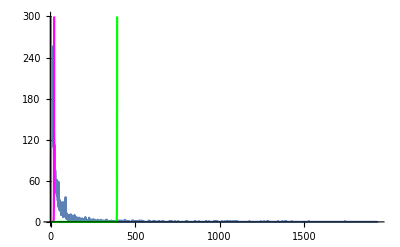

```mathematica
Show[p1,p2,p3]
```

```mathematica
Plots:
Data Plot:
```

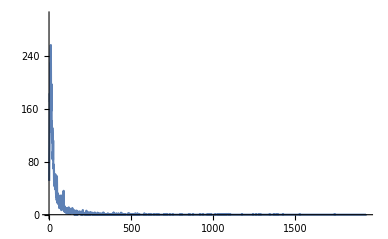

```mathematica
dataplot=ListLinePlot[Delete[degfreq,1],PlotRange->{0,300}]
```

```mathematica
logdeglist=Map[Log]
```

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.

```mathematica
LogLogPlot[dataplot]
```

LogLogPlot::argr: LogLogPlot called with 1 argument; 2 arguments are expected.

LogLogPlot[dataplot]

We want to test the following function for a good fit for our data set:

```mathematica
fit=Function[{a,b,k}, 	
	(k^a)*10^(k/b)];
```

Pairs (a,b):

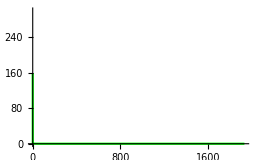

```mathematica
a1=-0.5;b1=-100;
p2=Plot[fit1[a1,b1,k],{k,0,1933},PlotRange->{{0,1933},{0,300}},PlotStyle->Green]
```

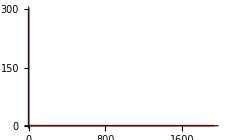

```mathematica
a1=-0.71;b1=-2167;
p3=Plot[fit1[a1,b1,k],{k,0,1933},PlotRange->{{0,1933},{0,300}},PlotStyle->Pink]
```

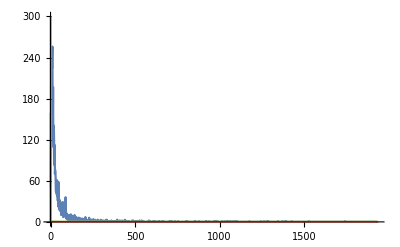

```mathematica
Show[dataplot,p2,p3]
```